```mathematica
SetDirectory[NotebookDirectory[]];
v = 4;
G = RandomGraph[{v,v},VertexLabels-> "Name"];
A = AdjacencyMatrix[G];
K = KirchhoffMatrix[G];
A//MatrixForm;
Export["adjmat.txt",A,"Table"];
l = Length[A];
```

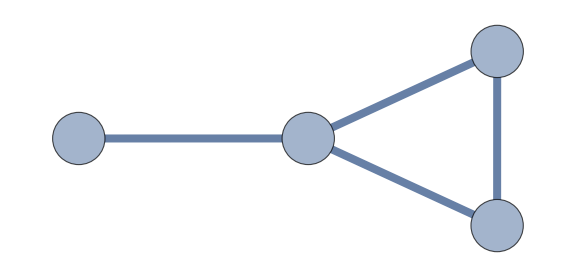

2qwalk_graph.png

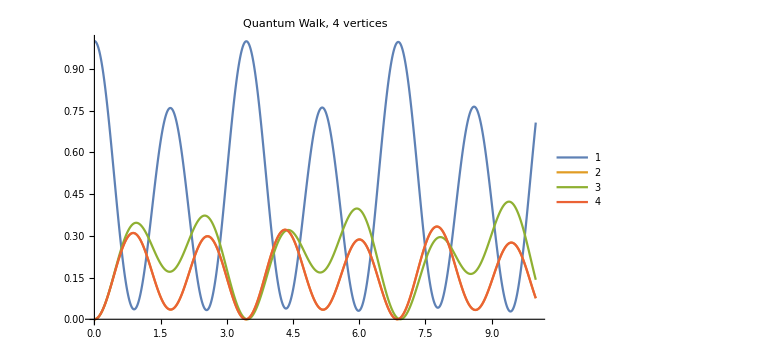
-Graphics-Time (seconds)Probability

2qwalk_mat.png

```mathematica
start = 0;
end = 10;
step = 0.01;
ψ0 = UnitVector[l,1];
ψ1[t_] := MatrixExp[-ⅈ A t,ψ0];
Graph[G,VertexSize->0.3,EdgeStyle-> {Thickness[.01]},VertexLabels-> Table[i->Placed[Text[i,BaseStyle-> {Large}],Center],{i,l}],ImageSize->Large]
Export["2qwalk_graph.png",%]
ListLinePlot[Table[Transpose[{Table[t,{t,start,end,step}],Table[Norm[ψ1[t][[i]]]^2,{t,start,end,step}]}],{i,l}],PlotLabel->Style["Quantum Walk, "<>ToString[v]<>" vertices",14,Bold],ImageSize->Large,PlotRange->Full,PlotLegends->Placed[Automatic,{0.9,0.8}]];
Labeled[%,{"Time (seconds)","Probability"},{Bottom,Left},RotateLabel->True]
Export["2qwalk_mat.png",%]
```

```mathematica
Manipulate[Graph[G,VertexSize->0.3,EdgeStyle-> {Thickness[.01]},VertexStyle-> Table[i-> GrayLevel[Norm[ψ1[t][[i]]]^2],{i,l}],VertexLabels-> Table[i->Placed[Text[i,BaseStyle-> {Large,Gray}],Center],{i,l}],ImageSize->Large],{t,0,10,0.1}]
```